Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

March 15, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Case Study: pKa Analysis of Nine Drugs

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of March 12, 2021, we evaluated 9 drug compounds to determine the pKa value, percent ionization and the solubility.

## Methodology

For this study, a dataset of the elPot values and the pKa values was collected from the NCSSM Canvas website. The following analyses were conducted:

Solubility for each drug was calculated by the empirical method and examining the functional groups of each molecule.

A regression analysis was performed to find the relationship between the elPot value and the pKa values.

The elPot values were calculated using computational chemistry methods.

The above regression was used to predict the pKa values.

Percent ionization was calculated for a range of pH values using the pKa value.

## Results

### Solubility

Each drug was analyzed using the empirical method to determine the level of solubility. If the ratio of soluble carbons/total carbons is less than 50%, then the drug is characterized as “Not soluble”. If the ratio is between 50-75%, the drug is “Slightly soluble”. If the ratio is greater than 75%, the drug is “Soluble”.

X1286: Soluble

X3489: Not Soluble

X6245: Slightly Soluble

X7131: Not Soluble

X2174: Slightly Soluble

X5689: Soluble

X6234: Soluble

X7111: Soluble

X1349: Not Soluble

### Regression Calculation

Using the parameters provided in the dataset above, we have built a regression model to predict pKa given the elPotMax value.

```mathematica
elPot = {0.0621, 0.09247, 0.09119, 0.07737, 0.08041, 0.08312};
pka = {1.23, 4.19, 3.51, 3.1, 4.7, 4.75};
togetherData = Transpose[{elPot,pka}];
myRegressionModel = LinearModelFit[togetherData,{elpotA},{elpotA}];
Print["Regression Model: pka = ", TraditionalForm[Normal[myRegressionModel]]]
```

Regression Model: pka = 88.8708 elpotA-3.62831

### Estimating pKa Values

Experimental elPot values were found by computational chemistry. The optimized chemistry of each molecule was imported, and a molecular orbital calculation was run with the model chemistry B3LYP and the basis set 3-21G. These values were fed into the above equation to predict the pKa value for each drug.

```mathematica
eplotExperimental = {0.1353, 0.1451, 0.1160, 0.1000, 0.0955, 0.1067, 0.1110, 0.1014, 0.0988};
drugNames = {"X1286", "X3489", "X6245", "X7131", "X2174", "X5689", "X6234", "X7111", "X1349"};
pkaPredicted =List[];
For[i=1,i<(Length[eplotExperimental]+1),i++,AppendTo[pkaPredicted,myRegressionModel[eplotExperimental[[i]]]]];
header = {"Drug Name", "Experimental ElPotMax Value","Predicted pKa Value"};
```

```mathematica
finalTable =Transpose[{drugNames,eplotExperimental,pkaPredicted}];
finalTable = Insert[finalTable,header,1];
```

```mathematica
Grid[finalTable, Frame -> All]
```

Drug Name | Experimental ElPotMax Value | Predicted pKa Value
X1286 | 0.1353 | 8.39591
X3489 | 0.1451 | 9.26684
X6245 | 0.116 | 6.6807
X7131 | 0.1 | 5.25877
X2174 | 0.0955 | 4.85885
X5689 | 0.1067 | 5.8542
X6234 | 0.111 | 6.23635
X7111 | 0.1014 | 5.38319
X1349 | 0.0988 | 5.15212

### Plotting Percent Ionization

Using the calculated pKa, the percent ionization for a pH range of 1 to 12 was calculated for each drug. This was done by using a modified version of the Henderson-Hasselbalch Equation. The values for each drug were plotted on a scatter plot, and the figures were combined into one graphic found below. As shown in these figures, each drug has variable percent ionization values for a range of pH values. Therefore, it is important to take in mind the pH of an environment to determine the correct mode of drug transport. Oral drugs and Intramuscular are mainly non-ionized while Subcutaneous drugs are mainly ionized. X7131, X2174, X711, and X1349 start ionizing around similar pH values in a range of 2-4.  X6245, X5689, and X6234 start ionizing around similar pH values in a range of 4-5.  X1286 and X3489 have significantly higher pKa values, and therefore start ionizing at a higher pH of around 6-8.

```mathematica
percentIon[phA_,pkaA_] := N[100/(1+10^(-(phA-pkaA)))];
```

```mathematica
drug1Plot = Plot[percentIon[x,pkaPredicted[[1]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X1286_Percent_Ionization]];
drug2Plot =Plot[percentIon[x,pkaPredicted[[2]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X3489_Percent_Ionization]];
drug3Plot = Plot[percentIon[x,pkaPredicted[[3]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X6245_Percent_Ionization]];
drug4Plot = Plot[percentIon[x,pkaPredicted[[4]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X7131_Percent_Ionization]];
drug5Plot = Plot[percentIon[x,pkaPredicted[[5]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X2174_Percent_Ionization]];
drug6Plot = Plot[percentIon[x,pkaPredicted[[6]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X5689_Percent_Ionization]];
drug7Plot = Plot[percentIon[x,pkaPredicted[[7]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X6234_Percent_Ionization]];
drug8Plot = Plot[percentIon[x,pkaPredicted[[8]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X7111_Percent_Ionization]];
drug9Plot = Plot[percentIon[x,pkaPredicted[[9]]], {x,1,12}, AxesLabel->{HoldForm[pH],HoldForm[Percent Ionization]},PlotLabel -> HoldForm[X1349_Percent_Ionization]];
```

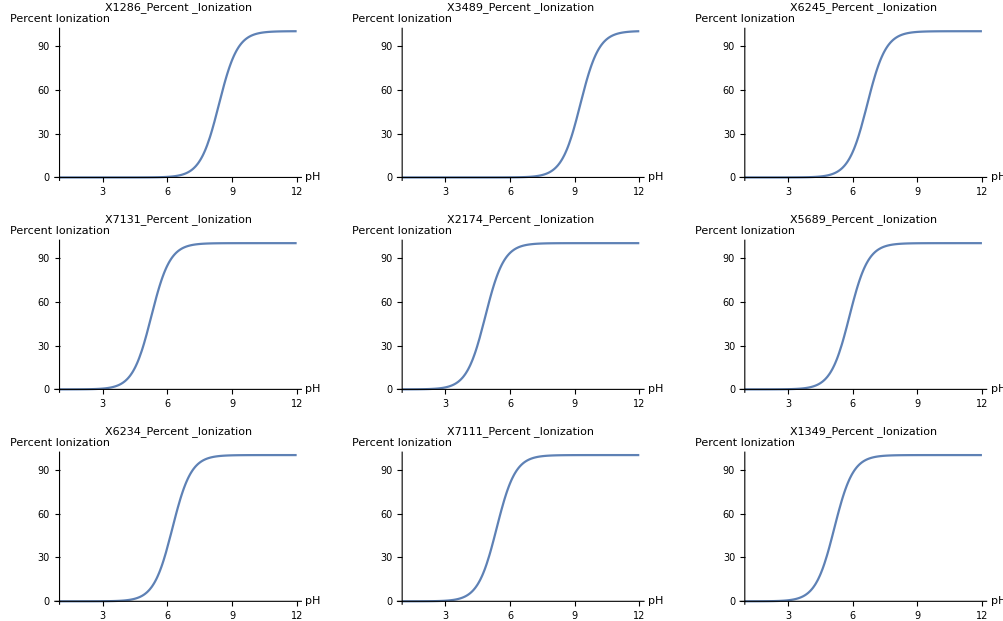

```mathematica
GraphicsGrid[{{drug1Plot,drug2Plot,drug3Plot},{drug4Plot,drug5Plot,drug6Plot},{drug7Plot,drug8Plot,drug9Plot}}]
```

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on March 15, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References: